```mathematica
Quit[];
```

```mathematica
Needs["QuantumManyBody`"]
```

```mathematica
latticeSize = 10;
length = 2^latticeSize;
```

```mathematica
listCouplings = Partition[Range @ latticeSize , 2 , 1 , 1];
```

```mathematica
listGraphCoefficients = {listCouplings , ({1 , 1 , 1} &) /@ Range @ Length @ listCouplings}
```

{{{1,2},{2,3},{3,4},{4,5},{5,6},{6,7},{7,8},{8,9},{9,10},{10,1}},{{1,1,1},{1,1,1},{1,1,1},{1,1,1},{1,1,1},{1,1,1},{1,1,1},{1,1,1},{1,1,1},{1,1,1}}}

```mathematica
{hamiltonianDecomposed , hamiltonian} = SpinChainHamiltonian @@ listGraphCoefficients;
```

```mathematica
groundState = Chop[FindGroundState @ hamiltonian, 10^-8];
groundEnergy = EnergyStored[groundState , hamiltonian]
```

-18.0618

```mathematica
β = 3.;
Δt = 0.1;
```

```mathematica
initialState = SparseArray[((Position[#,Min[#]]&) @ Normal @ Diagonal @ hamiltonian)[[1 ]] -> 1. , {2^latticeSize} , 0];
```

```mathematica
dD = 0;
```

```mathematica
tryEvolution = QITE[latticeSize , hamiltonianDecomposed , listCouplings , β , Δt , initialState , dD];
```

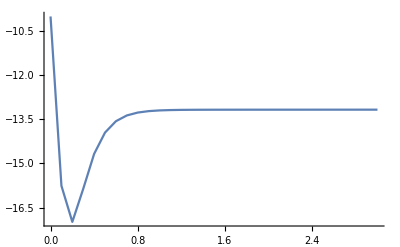

```mathematica
ListPlot[({#[[1]] , Conjugate @ #[[2]] . hamiltonian . #[[2]]} &)/@ tryEvolution , Joined->True , PlotRange->All]
```